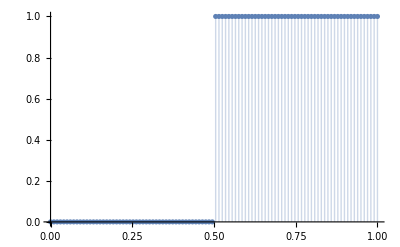
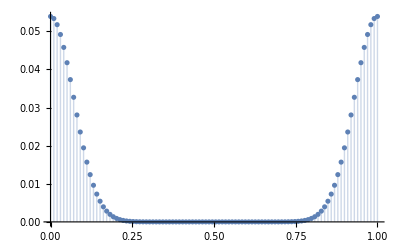

```mathematica
n=100;dx=1./(n-1);
a=Table[UnitStep[x-1/2],{x,0,1,dx}];
b=Table[If[x<=1/2,Exp[-100 x^2],Exp[-100 (1-x)^2]],{x,0,1,dx}];
b=b/Total[b];

{ListPlot[a,Filling->Axis,DataRange->{0,1}],ListPlot[b,Filling->Axis,PlotRange->All,DataRange->{0,1}]}
```